# Notebook for : Relativity Made Relatively Easy Volume 2: General Relativty and Cosmology by Andrew Steane

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 22, 2023

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper Books Volume 1 and Volume 2

```mathematica
Hyperlink["Relativity Made Relatively Easy Volume 2:  General Relativty and Cosmology by Andrew Steane",
"https://global.oup.com/academic/product/relativity-made-relatively-easy-volume-2-9780192893543?cc=us&lang=en&"]
```

[Relativity Made Relatively Easy Volume 2:  General Relativty and Cosmology by Andrew Steane](https://global.oup.com/academic/product/relativity-made-relatively-easy-volume-2-9780192893543?cc=us&lang=en&)

```mathematica
Hyperlink["Relativity Made Relatively Easy Volume 1",
"https://global.oup.com/academic/product/relativity-made-relatively-easy-9780199662869?lang=en&cc=us"]
```

[Relativity Made Relatively Easy Volume 1](https://global.oup.com/academic/product/relativity-made-relatively-easy-9780199662869?lang=en&cc=us)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 8 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[β]] , 
PasteButton[SubMinus[β]]  , 
PasteButton[Subscript[r,s]],
PasteButton[SubPlus[r]] , 
PasteButton[SubMinus[r]]  
}]
```

gn92g_shm31FrontEndObject[LinkObject["gn92g_shm", 3, 1]]31Untitled-2

```mathematica
Symbolize[β_+]
Symbolize[β_-]
Symbolize[Subscript[r, s]]
Symbolize[r_+]
Symbolize[r_-]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,  
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *) 
Subscript[r, s] /: Dt[Subscript[r, s]] = 0 ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 17.1: Schwarzschild Droste

```mathematica
Clear[eq17pt1]
eq17pt1 = 
- A[r] dt^2+B[r] dr^2+ r^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dt^2 A[r]+dr^2 B[r]+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric17pt1]
metric17pt1 = 
lineToMetric[eq17pt1 ,{dt,dr,dθ,dϕ}] ;
metric17pt1// MatrixForm // pdConv
```

(-A(r) | 0 | 0 | 0
0 | B(r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

## Euler Lagrange Equations Giving Geodesic Equations For Metric 17.1: Schwarzschild Droste Giving Equations 17.3 - 17.6

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric17pt1]
geodesicEquationsMetric17pt1 =
eulerLagrangeEquations[metric17pt1,{t,r,θ,ϕ},λ]  // Expand ;
geodesicEquationsMetric17pt1 // TableForm
```

t''[λ]==-(A'[r[λ]] r'[λ] t'[λ])/A[r[λ]]
r''[λ]==-(B'[r[λ]] r'[λ]^2)/(2 B[r[λ]])-(A'[r[λ]] t'[λ]^2)/(2 B[r[λ]])+(r[λ] θ'[λ]^2)/B[r[λ]]+(r[λ] Sin[θ[λ]]^2 ϕ'[λ]^2)/B[r[λ]]
θ''[λ]==-(2 r'[λ] θ'[λ])/r[λ]+Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2
ϕ''[λ]==-(2 r'[λ] ϕ'[λ])/r[λ]-2 Cot[θ[λ]] θ'[λ] ϕ'[λ]

```mathematica
Clear[geodesicEquationsMetric17pt1Reduced]
geodesicEquationsMetric17pt1Reduced = 
geodesicEquationsMetric17pt1 /. q_[λ] :> q  ;
geodesicEquationsMetric17pt1Reduced // TableForm
```

t''==-(r' t' A'[r])/A[r]
r''==(r (θ')^2)/B[r]+(r Sin[θ]^2 (ϕ')^2)/B[r]-((t')^2 A'[r])/(2 B[r])-((r')^2 B'[r])/(2 B[r])
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'

```mathematica
Clear[firstIntegrals17pt1]
firstIntegrals17pt1 = 
FirstIntegrals[ ℒ , q , λ ]   ;
firstIntegrals17pt1// TableForm
```

FirstIntegral[t]→2 A[r[λ]] t'[λ]
FirstIntegral[ϕ]→-2 r[λ]^2 Sin[θ[λ]]^2 ϕ'[λ]
FirstIntegral[λ]→B[r[λ]] r'[λ]^2-A[r[λ]] t'[λ]^2+r[λ]^2 (θ'[λ]^2+Sin[θ[λ]]^2 ϕ'[λ]^2)

```mathematica
Clear[firstIntegrals17pt1Reduced]
firstIntegrals17pt1Reduced = 
firstIntegrals17pt1 /.  q_[λ] :> q   ;
firstIntegrals17pt1Reduced // TableForm
```

FirstIntegral[t]→2 A[r] t'
FirstIntegral[ϕ]→-2 r^2 Sin[θ]^2 ϕ'
FirstIntegral→B[r] (r')^2-A[r] (t')^2+r^2 ((θ')^2+Sin[θ]^2 (ϕ')^2)

```mathematica
Clear[eq17pt3a]
eq17pt3a = 
ℒ  ;
eq17pt3a// pdConv
```

-A(r(λ)) ((∂t(λ))/(∂λ))^2+B(r(λ)) ((∂r(λ))/(∂λ))^2+(r(λ))^2 sin^2(θ(λ)) ((∂ϕ(λ))/(∂λ))^2+(r(λ))^2 ((∂θ(λ))/(∂λ))^2

```mathematica
Clear[eq17pt3]
eq17pt3 =
geodesicEquationsMetric17pt1Reduced[[1]]
```

t''==-(r' t' A'[r])/A[r]

```mathematica
Clear[eq17pt4]
eq17pt4 =
geodesicEquationsMetric17pt1Reduced[[2]]
```

r''==(r (θ')^2)/B[r]+(r Sin[θ]^2 (ϕ')^2)/B[r]-((t')^2 A'[r])/(2 B[r])-((r')^2 B'[r])/(2 B[r])

```mathematica
Clear[eq17pt5]
eq17pt5 =
geodesicEquationsMetric17pt1Reduced[[3]]
```

θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2

```mathematica
Clear[eq17pt6]
eq17pt6 =
geodesicEquationsMetric17pt1Reduced[[4]]
```

ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'

## Calculation of Tensors Associated With Metric 17.1: Schwarzschild Droste

```mathematica
Clear[input17pt1] 
input17pt1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList17pt1];
tensorList17pt1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList17pt1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList17pt1[[2]]  = 
ChristoffelSymbol[ tensorList17pt1[[1]] , ActWith-> Simplify] ;
tensorList17pt1[[3]] = 
RiemannTensor[ tensorList17pt1[[1]] , ActWithNested-> Simplify ];
tensorList17pt1[[4]] = 
RicciTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
tensorList17pt1[[5]] = 
RicciScalar[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
tensorList17pt1[[6]] = 
KretschmannScalar[ tensorList17pt1[[1]] , ActWith-> Simplify] ; 
tensorList17pt1[[7]] = 
EinsteinTensor[ tensorList17pt1[[1]] , ActWith-> Simplify] ;  
tensorList17pt1[[8]] = 
WeylTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
 tensorList17pt1[[9]] = 
CottonTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all 1.64  *) 
input17pt1[ "metric17pt1", metric17pt1, "SchwarzschildDroste","g^schw",{t,r,θ,ϕ}, "Greek"] // Timing
```

{2.83825,Null}

```mathematica
tensorList17pt1
```

{(g^schw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList17pt1[[1]] 
TensorName[tensorList17pt1[[1]]] 
TensorValues[tensorList17pt1[[1]]] // MatrixForm // pdConv
```

(g^schw)_αβ^

SchwarzschildDroste

(-A(r) | 0 | 0 | 0
0 | B(r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
tensorList17pt1[[2]] 
TensorName[tensorList17pt1[[2]]] 
TensorValues[tensorList17pt1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSchwarzschildDroste

((0
((∂A(r))/(∂r))/(2 A(r))
0
0) | (((∂A(r))/(∂r))/(2 A(r))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(((∂A(r))/(∂r))/(2 B(r))
0
0
0) | (0
((∂B(r))/(∂r))/(2 B(r))
0
0) | (0
0
-r/(B(r))
0) | (0
0
0
-(r sin^2(θ))/(B(r)))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList17pt1[[3]] 
TensorName[tensorList17pt1[[3]]] 
TensorValues[tensorList17pt1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSchwarzschildDroste

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 (-((∂A(r))/(∂r) (∂B(r))/(∂r))/(B(r))+2 (∂^2 A(r))/(∂r^2)-((∂A(r))/(∂r))^2/(A(r))) | 0 | 0
1/4 (((∂A(r))/(∂r) (∂B(r))/(∂r))/(B(r))-2 (∂^2 A(r))/(∂r^2)+((∂A(r))/(∂r))^2/(A(r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r (∂A(r))/(∂r))/(2 B(r)) | 0
0 | 0 | 0 | 0
-(r (∂A(r))/(∂r))/(2 B(r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (r sin^2(θ) (∂A(r))/(∂r))/(2 B(r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(r sin^2(θ) (∂A(r))/(∂r))/(2 B(r)) | 0 | 0 | 0)
(0 | 1/4 (((∂A(r))/(∂r) (∂B(r))/(∂r))/(B(r))-2 (∂^2 A(r))/(∂r^2)+((∂A(r))/(∂r))^2/(A(r))) | 0 | 0
1/4 (-((∂A(r))/(∂r) (∂B(r))/(∂r))/(B(r))+2 (∂^2 A(r))/(∂r^2)-((∂A(r))/(∂r))^2/(A(r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r (∂B(r))/(∂r))/(2 B(r)) | 0
0 | -(r (∂B(r))/(∂r))/(2 B(r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r sin^2(θ) (∂B(r))/(∂r))/(2 B(r))
0 | 0 | 0 | 0
0 | -(r sin^2(θ) (∂B(r))/(∂r))/(2 B(r)) | 0 | 0)
(0 | 0 | -(r (∂A(r))/(∂r))/(2 B(r)) | 0
0 | 0 | 0 | 0
(r (∂A(r))/(∂r))/(2 B(r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(r (∂B(r))/(∂r))/(2 B(r)) | 0
0 | (r (∂B(r))/(∂r))/(2 B(r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 (B(r)-1) sin^2(θ))/(B(r))
0 | 0 | -(r^2 (B(r)-1) sin^2(θ))/(B(r)) | 0)
(0 | 0 | 0 | -(r sin^2(θ) (∂A(r))/(∂r))/(2 B(r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(r sin^2(θ) (∂A(r))/(∂r))/(2 B(r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(r sin^2(θ) (∂B(r))/(∂r))/(2 B(r))
0 | 0 | 0 | 0
0 | (r sin^2(θ) (∂B(r))/(∂r))/(2 B(r)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 (B(r)-1) sin^2(θ))/(B(r))
0 | 0 | (r^2 (B(r)-1) sin^2(θ))/(B(r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[4]] 
TensorName[tensorList17pt1[[4]]] 
TensorValues[tensorList17pt1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSchwarzschildDroste

(((∂A(r))/(∂r) (4/r-((∂B(r))/(∂r))/(B(r)))+2 (∂^2 A(r))/(∂r^2)-((∂A(r))/(∂r))^2/(A(r)))/(4 B(r)) | 0 | 0 | 0
0 | (r B(r) (((∂A(r))/(∂r))^2-2 A(r) (∂^2 A(r))/(∂r^2))+A(r) (4 A(r)+r (∂A(r))/(∂r)) (∂B(r))/(∂r))/(4 r (A(r))^2 B(r)) | 0 | 0
0 | 0 | 1/2 (-((r (∂A(r))/(∂r))/(A(r))+2)/(B(r))+(r (∂B(r))/(∂r))/(B(r))^2+2) | 0
0 | 0 | 0 | (sin^2(θ) (A(r) (2 (B(r))^2-2 B(r)+r (∂B(r))/(∂r))-r B(r) (∂A(r))/(∂r)))/(2 A(r) (B(r))^2))

```mathematica
tensorList17pt1[[5]] 
TensorName[tensorList17pt1[[5]]] 
TensorValues[tensorList17pt1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSchwarzschildDroste

(r A(r) (r (∂A(r))/(∂r) (∂B(r))/(∂r)-2 B(r) (r (∂^2 A(r))/(∂r^2)+2 (∂A(r))/(∂r)))+r^2 B(r) ((∂A(r))/(∂r))^2+4 (A(r))^2 ((B(r))^2-B(r)+r (∂B(r))/(∂r)))/(2 r^2 (A(r))^2 (B(r))^2)

```mathematica
tensorList17pt1[[6]] 
TensorName[tensorList17pt1[[6]]] 
TensorValues[tensorList17pt1[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSchwarzschildDroste

(r^4 (B(r))^2 ((∂A(r))/(∂r))^4+8 (A(r))^4 (r^2 ((∂B(r))/(∂r))^2+2 (B(r))^4-4 (B(r))^3+2 (B(r))^2)+2 r^4 A(r) B(r) ((∂A(r))/(∂r))^2 ((∂A(r))/(∂r) (∂B(r))/(∂r)-2 B(r) (∂^2 A(r))/(∂r^2))+(A(r))^2 (r^4 ((∂A(r))/(∂r))^2 ((∂B(r))/(∂r))^2-4 r^4 B(r) (∂A(r))/(∂r) (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+4 (B(r))^2 (2 r^2 ((∂A(r))/(∂r))^2+r^4 ((∂^2 A(r))/(∂r^2))^2)))/(4 r^4 (A(r))^4 (B(r))^4)

```mathematica
tensorList17pt1[[7]] 
TensorName[tensorList17pt1[[7]]] 
TensorValues[tensorList17pt1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSchwarzschildDroste

((A(r) ((B(r))^2-B(r)+r (∂B(r))/(∂r)))/(r^2 (B(r))^2) | 0 | 0 | 0
0 | (A(r) (-B(r))+A(r)+r (∂A(r))/(∂r))/(r^2 A(r)) | 0 | 0
0 | 0 | (r (A(r) (2 B(r) (r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-r (∂A(r))/(∂r) (∂B(r))/(∂r))-2 (A(r))^2 (∂B(r))/(∂r)-r B(r) ((∂A(r))/(∂r))^2))/(4 (A(r))^2 (B(r))^2) | 0
0 | 0 | 0 | (r sin^2(θ) (A(r) (2 B(r) (r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-r (∂A(r))/(∂r) (∂B(r))/(∂r))-2 (A(r))^2 (∂B(r))/(∂r)-r B(r) ((∂A(r))/(∂r))^2))/(4 (A(r))^2 (B(r))^2))

```mathematica
tensorList17pt1[[8]] 
TensorName[tensorList17pt1[[8]]] 
TensorValues[tensorList17pt1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSchwarzschildDroste

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(12 r^2 A(r) B(r)) | 0 | 0
(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(12 r^2 A(r) B(r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 A(r) (B(r))^2) | 0
0 | 0 | 0 | 0
-(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 A(r) (B(r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 A(r) (B(r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 A(r) (B(r))^2) | 0 | 0 | 0)
(0 | (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(12 r^2 A(r) B(r)) | 0 | 0
-(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(12 r^2 A(r) B(r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 (A(r))^2 B(r)) | 0
0 | (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 (A(r))^2 B(r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 (A(r))^2 B(r))
0 | 0 | 0 | 0
0 | (sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 (A(r))^2 B(r)) | 0 | 0)
(0 | 0 | -(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 A(r) (B(r))^2) | 0
0 | 0 | 0 | 0
(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 A(r) (B(r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 (A(r))^2 B(r)) | 0
0 | -(r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r)))/(24 (A(r))^2 B(r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(12 (A(r))^2 (B(r))^2)
0 | 0 | (r^2 sin^2(θ) (-r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))-r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (-4 (B(r))^2+4 B(r)+2 r (∂B(r))/(∂r))))/(12 (A(r))^2 (B(r))^2) | 0)
(0 | 0 | 0 | -(sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 A(r) (B(r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 A(r) (B(r))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 (A(r))^2 B(r))
0 | 0 | 0 | 0
0 | -(sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(24 (A(r))^2 B(r)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 sin^2(θ) (-r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))-r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (-4 (B(r))^2+4 B(r)+2 r (∂B(r))/(∂r))))/(12 (A(r))^2 (B(r))^2)
0 | 0 | (r^2 sin^2(θ) (r A(r) (2 B(r) ((∂A(r))/(∂r)-r (∂^2 A(r))/(∂r^2))+r (∂A(r))/(∂r) (∂B(r))/(∂r))+r^2 B(r) ((∂A(r))/(∂r))^2+(A(r))^2 (4 (B(r))^2-4 B(r)-2 r (∂B(r))/(∂r))))/(12 (A(r))^2 (B(r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[9]] 
TensorName[tensorList17pt1[[9]]] 
TensorValues[tensorList17pt1[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSchwarzschildDroste

((0
(2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (2 r^2 B(r) (∂^2 B(r))/(∂r^2)-4 r^2 ((∂B(r))/(∂r))^2-4 (B(r))^3+4 (B(r))^2)-r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (-r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))+2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2))-4 (∂A(r))/(∂r))))/(6 r^3 (A(r))^2 (B(r))^3)
0
0) | ((-2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (-2 r^2 B(r) (∂^2 B(r))/(∂r^2)+4 r^2 ((∂B(r))/(∂r))^2+4 (B(r))^3-4 (B(r))^2)+r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))-2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (4 (∂A(r))/(∂r)-2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2)))))/(6 r^3 (A(r))^2 (B(r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
(-2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (-2 r^2 B(r) (∂^2 B(r))/(∂r^2)+4 r^2 ((∂B(r))/(∂r))^2+4 (B(r))^3-4 (B(r))^2)+r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))-2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (4 (∂A(r))/(∂r)-2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2)))))/(12 r (A(r))^3 (B(r))^3)
0) | (0
(2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (2 r^2 B(r) (∂^2 B(r))/(∂r^2)-4 r^2 ((∂B(r))/(∂r))^2-4 (B(r))^3+4 (B(r))^2)-r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (-r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))+2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2))-4 (∂A(r))/(∂r))))/(12 r (A(r))^3 (B(r))^3)
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
(sin^2(θ) (-2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (-2 r^2 B(r) (∂^2 B(r))/(∂r^2)+4 r^2 ((∂B(r))/(∂r))^2+4 (B(r))^3-4 (B(r))^2)+r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))-2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (4 (∂A(r))/(∂r)-2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2))))))/(12 r (A(r))^3 (B(r))^3)) | (0
0
0
0) | (0
-(sin^2(θ) (-2 r^3 (B(r))^2 ((∂A(r))/(∂r))^3+(A(r))^3 (-2 r^2 B(r) (∂^2 B(r))/(∂r^2)+4 r^2 ((∂B(r))/(∂r))^2+4 (B(r))^3-4 (B(r))^2)+r^2 A(r) B(r) (∂A(r))/(∂r) (B(r) (4 r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-2 r (∂A(r))/(∂r) (∂B(r))/(∂r))+r (A(r))^2 (r B(r) (3 r (∂^2 A(r))/(∂r^2) (∂B(r))/(∂r)+(∂A(r))/(∂r) (r (∂^2 B(r))/(∂r^2)+(∂B(r))/(∂r)))-2 r^2 (∂A(r))/(∂r) ((∂B(r))/(∂r))^2+(B(r))^2 (4 (∂A(r))/(∂r)-2 r (r (∂^3 A(r))/(∂r^3)+2 (∂^2 A(r))/(∂r^2))))))/(12 r (A(r))^3 (B(r))^3)
0
0))

## Derivation of Vacuum Field Equations For Metric 17.1: Schwarzschild Droste (Not Finished)

```mathematica
Clear[nonzeroRicci17pt1] 
nonzeroRicci17pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList17pt1[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci17pt1 // TableForm // pdConv
```

((∂A(r))/(∂r) (4/r-((∂B(r))/(∂r))/(B(r)))+2 (∂^2 A(r))/(∂r^2)-((∂A(r))/(∂r))^2/(A(r)))/(4 B(r))
(r B(r) (((∂A(r))/(∂r))^2-2 A(r) (∂^2 A(r))/(∂r^2))+A(r) (4 A(r)+r (∂A(r))/(∂r)) (∂B(r))/(∂r))/(4 r (A(r))^2 B(r))
1/2 (-((r (∂A(r))/(∂r))/(A(r))+2)/(B(r))+(r (∂B(r))/(∂r))/(B(r))^2+2)
(sin^2(θ) (A(r) (2 (B(r))^2-2 B(r)+r (∂B(r))/(∂r))-r B(r) (∂A(r))/(∂r)))/(2 A(r) (B(r))^2)

```mathematica
Clear[nonzeroEinstein17pt1] 
nonzeroEinstein17pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList17pt1[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein17pt1 // TableForm // pdConv
```

(A(r) ((B(r))^2-B(r)+r (∂B(r))/(∂r)))/(r^2 (B(r))^2)
(A(r) (-B(r))+A(r)+r (∂A(r))/(∂r))/(r^2 A(r))
(r (A(r) (2 B(r) (r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-r (∂A(r))/(∂r) (∂B(r))/(∂r))-2 (A(r))^2 (∂B(r))/(∂r)-r B(r) ((∂A(r))/(∂r))^2))/(4 (A(r))^2 (B(r))^2)
(r sin^2(θ) (A(r) (2 B(r) (r (∂^2 A(r))/(∂r^2)+(∂A(r))/(∂r))-r (∂A(r))/(∂r) (∂B(r))/(∂r))-2 (A(r))^2 (∂B(r))/(∂r)-r B(r) ((∂A(r))/(∂r))^2))/(4 (A(r))^2 (B(r))^2)

```mathematica
tensorList17pt1[[4]]
```

R_βγ^

```mathematica
Clear[eq17pt11a]
eq17pt11a = { 
SubPlus[β] == (D[A[r],r]/A[r] +D[B[r],r]/B[r]) , 
SubMinus[β] ==  (D[A[r],r]/A[r] -D[B[r],r]/B[r])
} ;
eq17pt11a  // TableForm
```

β_+==A'[r]/A[r]+B'[r]/B[r]
β_-==A'[r]/A[r]-B'[r]/B[r]

```mathematica
Clear[betaPlusReplace]
betaPlusReplace = 
Flatten[Solve[eq17pt11a[[1]] ,D[B[r],r]]][[1]]
```

B'[r]→(B[r] (β_+ A[r]-A'[r]))/A[r]

```mathematica
Clear[betaMinusReplace]
betaMinusReplace = 
Flatten[Solve[eq17pt11a[[2]] ,D[B[r],r]]][[1]]
```

B'[r]→-(B[r] (β_- A[r]-A'[r]))/A[r]

```mathematica
(* Currently too lazy to reduce these to exactly 17.11 *) 

tensorList17pt1[[4]][-μ,-ν]

Clear[eq17pt11b]
eq17pt11b = {
tensorList17pt1[[4]][-t,-t]  , 
tensorList17pt1[[4]][-r,-r]  , 
tensorList17pt1[[4]][-θ,-θ]  , 
tensorList17pt1[[4]][-ϕ,-ϕ] 
} // Expand  ;
eq17pt11b  // TableForm
```

R_μν^

A'[r]/(r B[r])-A'[r]^2/(4 A[r] B[r])-(A'[r] B'[r])/(4 B[r]^2)+A''[r]/(2 B[r])
A'[r]^2/(4 A[r]^2)+B'[r]/(r B[r])+(A'[r] B'[r])/(4 A[r] B[r])-A''[r]/(2 A[r])
1-1/B[r]-(r A'[r])/(2 A[r] B[r])+(r B'[r])/(2 B[r]^2)
Sin[θ]^2-Sin[θ]^2/B[r]-(r Sin[θ]^2 A'[r])/(2 A[r] B[r])+(r Sin[θ]^2 B'[r])/(2 B[r]^2)

## Derivation of Schwarzschild Droste Metric 17.15 (Equations 17.11 - 17.15)

```mathematica
Clear[eq17pt11c]
eq17pt11c = 
Expand[r*(B[r]/A[r])*tensorList17pt1[[4]][-t,-t]]+Expand[r*tensorList17pt1[[4]][-r,-r]  ] == 0
```

A'[r]/A[r]+B'[r]/B[r]==0

```mathematica
(* This just shows that takes the derivative of the product of A and B is equivalent to the expression above... *) 

Assuming[ A[r] B[r]!= 0 , DivideSides[
D[A[r] B[r],r] == 0  , A[r] B[r] ]] // Expand
```

A'[r]/A[r]+B'[r]/B[r]==0

```mathematica
Clear[eq17pt11d]
eq17pt11d = 
B[r] == c^2/A[r]
```

B[r]==c^2/A[r]

```mathematica
Clear[bDerivatives]
bDerivatives= { 
eq17pt11d  , 
D[eq17pt11d ,r]
}  /. Equal-> Rule ;
bDerivatives // TableForm
```

B[r]→c^2/A[r]
B'[r]→-(c^2 A'[r])/A[r]^2

```mathematica
tensorList17pt1[[4]]
Expand[tensorList17pt1[[4]][-θ,-θ]]

Expand[tensorList17pt1[[4]][-θ,-θ]] /. bDerivatives
```

R_βγ^

1-1/B[r]-(r A'[r])/(2 A[r] B[r])+(r B'[r])/(2 B[r]^2)

1-A[r]/c^2-(r A'[r])/c^2

```mathematica
Flatten[DSolve[( Expand[tensorList17pt1[[4]][-θ,-θ]] /. bDerivatives ) ==0 , A[r],r]][[1]] /. Rule-> Equal
```

A[r]==c^2+C[1]/r

```mathematica
Clear[eq17pt11e]
eq17pt11e = 
Collect[ ( Flatten[DSolve[( Expand[tensorList17pt1[[4]][-θ,-θ]] /. bDerivatives ) ==0 , A[r],r]][[1]] /. Rule-> Equal  ) /. C[1]-> (-1)*c^2 Subscript[r, s] , c^2]
```

A[r]==c^2 (1-r_s/r)

```mathematica
Clear[abReplace]
abReplace = { 
eq17pt11e /. Equal-> Rule    , 
( bDerivatives[[1]] /. (eq17pt11e  /. Equal-> Rule ) ) 
} ;
abReplace // TableForm
```

A[r]→c^2 (1-r_s/r)
B[r]→1/(1-r_s/r)

```mathematica
Clear[abDerivatives]
abDerivatives = { 
abReplace , 
D[abReplace,r] , 
D[abReplace,{r,2}] 
} // Flatten ;
abDerivatives // TableForm
```

A[r]→c^2 (1-r_s/r)
B[r]→1/(1-r_s/r)
A'[r]→(c^2 r_s)/r^2
B'[r]→-r_s/(r^2 (1-r_s/r)^2)
A''[r]→-(2 c^2 r_s)/r^3
B''[r]→(2 r_s^2)/(r^4 (1-r_s/r)^3)+(2 r_s)/(r^3 (1-r_s/r)^2)

```mathematica
eq17pt1

Clear[eq17pt12]
eq17pt12 = 
eq17pt1 /. (eq17pt11e  /. Equal-> Rule )  /. ( bDerivatives[[1]] /. (eq17pt11e  /. Equal-> Rule ) )
```

-dt^2 A[r]+dr^2 B[r]+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

dr^2/(1-r_s/r)-c^2 dt^2 (1-r_s/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[eq17pt13]
eq17pt13 = 
Subscript[r, s] == (2 G M)/c^2
```

r_s==(2 G M)/c^2

```mathematica
Clear[eq17pt14]
eq17pt14 = 
m == (G M)/c^2
```

m==(G M)/c^2

```mathematica
Clear[schwarzschildRadiusReplace]
schwarzschildRadiusReplace = 
Flatten[Solve[Eliminate[{eq17pt13 , eq17pt14 },M][[1]],Subscript[r, s]]][[1]]
```

r_s→2 m

```mathematica
Clear[eq17pt15]
eq17pt15 = 
eq17pt12  /.schwarzschildRadiusReplace
```

dr^2/(1-(2 m)/r)-c^2 dt^2 (1-(2 m)/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric17pt15]
metric17pt15 = 
lineToMetric[eq17pt15,{dt,dr,dθ,dϕ}] ;
metric17pt15 // MatrixForm // pdConv
```

(-c^2 (1-(2 m)/r) | 0 | 0 | 0
0 | 1/(1-(2 m)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

## Orbit Equations For Schwarzschild (17.17 - 17.20 - Be sure to check 17.20 to see if constants are in correct place)

```mathematica
Clear[eq17pt17]
eq17pt17 = 
DivideSides[( firstIntegrals17pt1Reduced[[1]][[2]] /. abReplace ) == 2 ℰ,2] /. schwarzschildRadiusReplace
```

c^2 (1-(2 m)/r) t'==ℰ

```mathematica
Clear[eq17pt18]
eq17pt18 = 
geodesicEquationsMetric17pt1Reduced[[3]]
```

θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2

```mathematica
Clear[eq17pt19]
eq17pt19 = 
DivideSides[ firstIntegrals17pt1Reduced[[2]][[2]] == - 2 L , -2 ]
```

r^2 Sin[θ]^2 ϕ'==L

```mathematica
Clear[tPrimePhiPrimeReplace]
tPrimePhiPrimeReplace = { 
Flatten[Solve[ eq17pt17 , t']][[1]] , 
Flatten[Solve[eq17pt19 ,  ϕ']][[1]]
} ;
tPrimePhiPrimeReplace // TableForm
```

t'→-(r ℰ)/(c^2 (2 m-r))
ϕ'→(L Csc[θ]^2)/r^2

```mathematica
(* ℒ could be set equal to +/- 1 or zero depending on timelike, spacelike or null geodesics - I think in their units this is c^2 ?? *) 

firstIntegrals17pt1Reduced[[3]][[2]]==-c^2
firstIntegrals17pt1Reduced[[3]][[2]]==-c^2 /. tPrimePhiPrimeReplace  /. abReplace
firstIntegrals17pt1Reduced[[3]][[2]] ==-c^2/. tPrimePhiPrimeReplace   /. abReplace /. schwarzschildRadiusReplace
```

B[r] (r')^2-A[r] (t')^2+r^2 ((θ')^2+Sin[θ]^2 (ϕ')^2)==-c^2

-(r^2 (1-r_s/r) ℰ^2)/(c^2 (2 m-r)^2)+(r')^2/(1-r_s/r)+r^2 ((L^2 Csc[θ]^2)/r^4+(θ')^2)==-c^2

-((1-(2 m)/r) r^2 ℰ^2)/(c^2 (2 m-r)^2)+(r')^2/(1-(2 m)/r)+r^2 ((L^2 Csc[θ]^2)/r^4+(θ')^2)==-c^2

```mathematica
Clear[eq17pt20]
eq17pt20 = 
Assuming[ (1-(2 m)/r)  != 0 , MultiplySides[ 
( firstIntegrals17pt1Reduced[[3]][[2]] ==-c^2/. tPrimePhiPrimeReplace   /. abReplace /. schwarzschildRadiusReplace ) , (1-(2 m)/r)  ] ] // Expand   // Simplify
```

(L^2 Csc[θ]^2)/r^2+(r')^2+r (-2 m+r) (θ')^2==c^2 (-1+(2 m)/r)+ℰ^2/c^2+(2 L^2 m Csc[θ]^2)/r^3

## Effective Potential For Equatorial Plane Giving Figure 17.1 Page 234

```mathematica
Clear[eq17pt21]
eq17pt21 = {
θ == π/2 , 
θ' == 0 , 
θ'' == 0 
} /. Equal-> Rule ;
eq17pt21  // TableForm
```

θ→π/2
θ'→0
θ''→0

```mathematica
(* Too lazy to do this right now... move terms, collect and call one group Veff to get next line...  *) 

Expand[DivideSides[ ( eq17pt20 /. eq17pt21  ),2]]
```

L^2/(2 r^2)+(r')^2/2==-c^2/2+(L^2 m)/r^3+(c^2 m)/r+ℰ^2/(2 c^2)

```mathematica
Clear[eq17pt22]
eq17pt22 = 
Veff = (1-(2 m)/r)(L^2/(2 r^2)) -((m c^2)/r)
```

(L^2 (1-(2 m)/r))/(2 r^2)-(c^2 m)/r

```mathematica
eq17pt22 // Expand
```

-(L^2 m)/r^3+L^2/(2 r^2)-(c^2 m)/r

```mathematica
Clear[xReplace]
xReplace =
Flatten[Solve[ x == r/m , r ] ][[1]]
```

r→m x

```mathematica
eq17pt22   /. xReplace /. L-> √12 m c  /. c-> 1  // Expand
```

-12/x^3+6/x^2-1/x

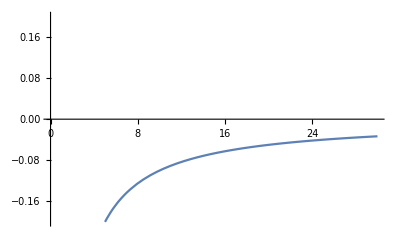

```mathematica
Clear[lEqualsZeroPlot]
lEqualsZeroPlot = 
Plot[ (eq17pt22   /. xReplace /. L-> 0/. c-> 1  // Expand ) , {x,0,30} , PlotRange-> {-0.2,0.2}]
```

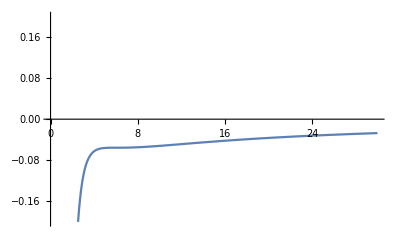

```mathematica
Clear[lEqualsRootTwelvePlot]
lEqualsRootTwelvePlot = 
Plot[ (eq17pt22   /. xReplace /. L-> √12 m c  /. c-> 1  // Expand ) , {x,0,30} , PlotRange-> {-0.2,0.2}]
```

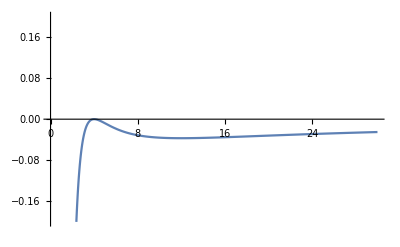

```mathematica
Clear[lEqualsFourPlot]
lEqualsFourPlot = 
Plot[ (eq17pt22   /. xReplace /. L->4 m c  /. c-> 1  // Expand ) , {x,0,30} , PlotRange-> {-0.2,0.2}]
```

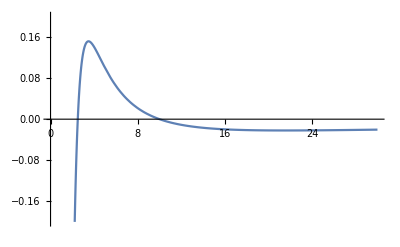

```mathematica
Clear[lEqualsFivePlot]
lEqualsFivePlot = 
Plot[ (eq17pt22   /. xReplace /. L->5 m c  /. c-> 1  // Expand ) , {x,0,30} , PlotRange-> {-0.2,0.2}]
```

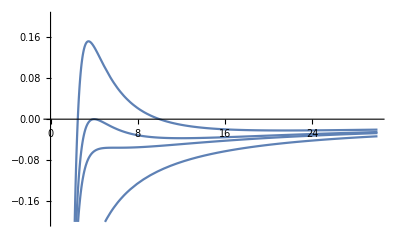

```mathematica
(* Add labels to this later... *) 

Clear[figure17pt1Page234]
figure17pt1Page234 = 
Show[lEqualsZeroPlot,lEqualsRootTwelvePlot,lEqualsFourPlot,lEqualsFivePlot]
```

## Inner Most Stable Circular Orbit Under Equation 17.23

```mathematica
Clear[eq17pt23]
eq17pt23 = 
Expand[r^4*D[eq17pt22,r]]==0
```

3 L^2 m-L^2 r+c^2 m r^2==0

```mathematica
(* Take a look at the root structure *) 

Flatten[Solve[eq17pt23 ,r]][[2]]
Flatten[Solve[eq17pt23 ,r]][[1]]
```

r→(L^2+√(L^4-12 c^2 L^2 m^2))/(2 c^2 m)

r→(L^2-√(L^4-12 c^2 L^2 m^2))/(2 c^2 m)

```mathematica
Flatten[Solve[L^4-12 c^2 L^2 m^2 ==0,L] ]// TableForm
```

L→0
L→0
L→-2 √3 c m
L→2 √3 c m

```mathematica
Flatten[Solve[L^4-12 c^2 L^2 m^2 ==0,L]][[4]]
```

L→2 √3 c m

```mathematica
Clear[rISCO]
rISCO = 
Flatten[Solve[eq17pt23 ,r]][[2]] /. Flatten[Solve[L^4-12 c^2 L^2 m^2 ==0,L]][[4]] /. Rule-> Equal
```

r==6 m

## Radial Worldlines (Not Finished) Starting Equation 17.24

```mathematica
{eq17pt17,eq17pt18,eq17pt19,eq17pt20} // TableForm
```

c^2 (1-(2 m)/r) t'==ℰ
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
r^2 Sin[θ]^2 ϕ'==L
(L^2 Csc[θ]^2)/r^2+(r')^2+r (-2 m+r) (θ')^2==c^2 (-1+(2 m)/r)+ℰ^2/c^2+(2 L^2 m Csc[θ]^2)/r^3

```mathematica
Clear[radialWorldlines]
radialWorldlines = {
eq17pt21 , 
  ϕ->constant,
ϕ'->0,
ϕ''->0
} // Flatten ;
radialWorldlines  // TableForm
```

θ→π/2
θ'→0
θ''→0
ϕ→constant
ϕ'→0
ϕ''→0

```mathematica
Clear[radialGeodesicEquations]
radialGeodesicEquations = 
 DeleteCases[{eq17pt17,eq17pt18,eq17pt19,eq17pt20} /. radialWorldlines ,True] ;
radialGeodesicEquations  // TableForm
```

c^2 (1-(2 m)/r) t'==ℰ
0==L
L^2/r^2+(r')^2==c^2 (-1+(2 m)/r)+(2 L^2 m)/r^3+ℰ^2/c^2

```mathematica
Clear[eq17pt24]
eq17pt24 = 
radialGeodesicEquations [[1]]
```

c^2 (1-(2 m)/r) t'==ℰ

```mathematica
Clear[eq17pt25]
eq17pt25 = 
Expand[Eliminate[radialGeodesicEquations [[2;;3]],L][[1]]]
```

ℰ^2==c^4-(2 c^4 m)/r+c^2 (r')^2

```mathematica
Clear[droppedFromRest]
droppedFromRest = 
ℰ == c^2
```

ℰ==c^2

```mathematica
(* pick the negative root.... since this is infalling we want the radial coordinate to DECREASE NOT INCREASE which would be the other root *) 

Clear[eq17pt26]
eq17pt26 = 
Flatten[Solve[( eq17pt25 /. ( droppedFromRest  /. Equal-> Rule ) ),r']][[1]] /. Rule-> Equal
```

r'==-(√2 c √m)/(√r)

```mathematica
Clear[dtdlambda]
dtdlambda = 
( Flatten[Solve[eq17pt24,t']][[1]] /. Rule-> Equal  ) /. (droppedFromRest  /. Equal-> Rule )
```

t'==-r/(2 m-r)

```mathematica
(* Will compare our derivation with that in book... *) 

Clear[eq17pt27OurDerivation]
eq17pt27OurDerivation = 
Assuming[ t'≠0,DivideSides[eq17pt26 ,dtdlambda]]
```

r'/t'==(√2 c √m (2 m-r))/r^(3/2)

```mathematica
(* Will compare this with above derivation *) 

Clear[eq17pt27TypedIn]
eq17pt27TypedIn = 
-c(1-(2 m)/r)√((2 m)/r)
```

-√2 c (1-(2 m)/r) √(m/r)

```mathematica
eq17pt27OurDerivation[[2]]   // Expand 
eq17pt27TypedIn  //PowerExpand // Expand
```

(2 √2 c m^(3/2))/r^(3/2)-(√2 c √m)/(√r)

(2 √2 c m^(3/2))/r^(3/2)-(√2 c √m)/(√r)

```mathematica
(* they just look different... and the key is to power expand so that the root structure eventually simplifies *) 

(eq17pt27OurDerivation[[2]]   // Expand )==(eq17pt27TypedIn  //PowerExpand // Expand )
```

True

```mathematica
(* Here we cheat with the differentials... *) 

 Clear[radialODE]
radialODE = 
(dr/dt) == -c(1-(2 m)/r)√((2 m)/r)  // PowerExpand // Expand
```

dr/dt==(2 √2 c m^(3/2))/r^(3/2)-(√2 c √m)/(√r)

```mathematica
(* entirely too lazy to do this... *) 

Clear[radialODEseperated]
radialODEseperated = 
ApplySides[FullSimplify,Assuming[dt!=0 , MultiplySides[Assuming[ radialODE[[2]]!= 0 , DivideSides[radialODE ,radialODE[[2]]]],dt]]]
```

(dr r^(3/2))/(√2 √m (2 c m-c r))==dt

## Orbit Precession Equation 17.37 (Redo this)

```mathematica
Clear[eq17pt37]
eq17pt37 = 
D[u[ϕ],{ϕ,2}] == - u[ϕ] + 3 m u[ϕ]^2 +(m c^2)/L^2
```

u''[ϕ]==(c^2 m)/L^2-u[ϕ]+3 m u[ϕ]^2

```mathematica
Clear[eq17pt39]
eq17pt39 = 
ϵ == ((3 m^2 c^2)/L^2)
```

ϵ==(3 c^2 m^2)/L^2

```mathematica
Clear[ellipticityAngularMomentum]
ellipticityAngularMomentum = 
Assuming[ϵ!= 0 , DivideSides[Assuming[ L^2!= 0 , MultiplySides[eq17pt39,L^2]],ϵ]]
```

L^2==(3 c^2 m^2)/ϵ

```mathematica
PowerExpand[ApplySides[Sqrt,ellipticityAngularMomentum ]] /. Equal-> Rule
```

L→(√3 c m)/(√ϵ)

```mathematica
eq17pt37 /. ( ellipticityAngularMomentum /. Equal-> Rule ) /.(  PowerExpand[ApplySides[Sqrt,ellipticityAngularMomentum ]] /. Equal-> Rule  )   /. m-> 1
```

u''[ϕ]==ϵ/3-u[ϕ]+3 u[ϕ]^2

## Circular Orbits (Not Finished) Equation 17.41

```mathematica
Clear[eq17pt41a]
eq17pt41a = { 
( Flatten[Solve[ ( eq17pt23 /. L^2-> elleSquared ) ,elleSquared ]][[1]] /. elleSquared->  L^2 ) /. Rule-> Equal  , 
r' == 0 
} ;
eq17pt41a // TableForm
```

L^2==-(c^2 m r^2)/(3 m-r)
r'==0

```mathematica
Clear[eq17pt41b]
eq17pt41b = 
(  Flatten[Solve[ ( ( eq17pt20 /. (eq17pt41a  /. Equal-> Rule ) /. radialWorldlines )  /. ℰ^2-> energySquared ) ,  energySquared]][[1]] /. Rule-> Equal  ) /.  energySquared-> ℰ^2 // Expand
```

ℰ^2==(4 c^4 m)/(3 m-r)-(4 c^4 m^2)/((3 m-r) r)-(c^4 r)/(3 m-r)

```mathematica
(* Without further assumptions taking the square root will introduce an imaginary number so we leave like this... *) 

Clear[eq17pt41]
eq17pt41 = 
ApplySides[Simplify,eq17pt41b ]
```

ℰ^2==-(c^4 (-2 m+r)^2)/((3 m-r) r)

## Photon Motion (Not Finished) Equations 17.57 - 17.62 (Redo plots)

```mathematica
Clear[eq17pt57]
eq17pt57 = 
Assuming[ 2 c^2!= 0, DivideSides[( firstIntegrals17pt1Reduced[[1]][[2]] /. abReplace /. schwarzschildRadiusReplace ) == 2 c^2 k ,2 c^2]]
```

(1-(2 m)/r) t'==k

```mathematica
Clear[eq17pt58]
eq17pt58 = 
DivideSides[( firstIntegrals17pt1Reduced[[2]][[2]] /. eq17pt21 ) == - 2 h ,-2]
```

r^2 ϕ'==h

```mathematica
Clear[tPrimePhiPrimeNullReplace]
tPrimePhiPrimeNullReplace = { 
Flatten[Solve[eq17pt57 , t']][[1]] , 
Flatten[Solve[eq17pt58 ,ϕ']][[1]]
} ;
tPrimePhiPrimeNullReplace // TableForm
```

t'→-(k r)/(2 m-r)
ϕ'→h/r^2

```mathematica
Clear[eq17pt59a]
eq17pt59a  = 
( firstIntegrals17pt1Reduced[[3]][[2]] /. abReplace /. schwarzschildRadiusReplace  /. eq17pt21 ) == 0
```

(r')^2/(1-(2 m)/r)-c^2 (1-(2 m)/r) (t')^2+r^2 (ϕ')^2==0

```mathematica
Clear[eq17pt59]
eq17pt59  = 
Assuming[ 1-(2 m)/r != 0 , MultiplySides[( eq17pt59a  /. tPrimePhiPrimeNullReplace  ),1-(2 m)/r]] // Expand // Simplify // Expand
```

-(2 h^2 m)/r^3+h^2/r^2+(r')^2==c^2 k^2

```mathematica
Clear[eq17pt60a]
eq17pt60a = 
k^2 c^2 == h^2/b^2
```

c^2 k^2==h^2/b^2

```mathematica
Flatten[Solve[eq17pt60a ,k]][[2]]
```

k→h/(b c)

```mathematica
Clear[eq17pt60]
eq17pt60 = 
eq17pt59  /. Flatten[Solve[eq17pt60a ,k]][[2]]
```

-(2 h^2 m)/r^3+h^2/r^2+(r')^2==h^2/b^2

```mathematica
eq17pt60 /. h-> 1
```

-(2 m)/r^3+1/r^2+(r')^2==1/b^2

```mathematica
Clear[eq17pt61,Veff]
eq17pt61 = 
Veff[r] == (eq17pt60 /. h-> 1 )[[1]][[1;;2]]
```

Veff[r]==-(2 m)/r^3+1/r^2

```mathematica
D[eq17pt61 ,r] 
D[eq17pt61 ,r] [[2]]==0
```

Veff'[r]==(6 m)/r^4-2/r^3

(6 m)/r^4-2/r^3==0

```mathematica
Clear[lightSphereRadius]
lightSphereRadius = 
Flatten[Solve[ D[eq17pt61 ,r] [[2]]==0 ,r]][[1]]
```

r→3 m

```mathematica
Vmax == ( eq17pt61[[2]] /. lightSphereRadius  )
```

Vmax==1/(27 m^2)

```mathematica
Clear[eq17pt62]
eq17pt62 = 
D[u[ϕ],{ϕ,2}] == u[ϕ](3 m u[ϕ]-1)
```

u''[ϕ]==u[ϕ] (-1+3 m u[ϕ])

```mathematica
Clear[uSolution]
uSolution = 
Flatten[NDSolve[{ ( eq17pt62  /. m-> 1 ),u[0] == 1 ,u'[0] == 1 } , u,{ϕ,0,1}]][[1]]
```

u→InterpolatingFunction[…]

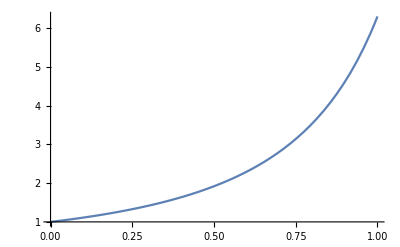

```mathematica
Plot[Evaluate[ u[ϕ] /. uSolution ],{ϕ,0,1}]
```

## (check this to make sure minus sign is in right place for tensorList[[1]] and difference in terms !!! ) Four Velocity u , Stress Energy of Perfect Fluid and its Covariant Divergence

```mathematica
PowerExpand[Sqrt[(-1)*(c^2)*tensorList17pt1[[1]][-t,-t]]]
```

c √A[r]

```mathematica
Clear[u]
u = ToTensor[ "u" , tensorList17pt1[[1]] , { PowerExpand[Sqrt[(-1)*(c^2)*tensorList17pt1[[1]][-t,-t]]],0,0,0} , {-μ}]
```

u_μ^

```mathematica
(* We need this to be - c^2 *) 

u[μ]u[-μ]
MergeTensors[u[μ]u[-μ]]
TensorValues[MergeTensors[u[μ]u[-μ]]] // Expand // Simplify
```

u_μ^ u_^μ

(u·u)

-c^2

```mathematica
u[-μ]u[-ν]
MergeTensors[u[-μ]u[-ν]]
TensorValues[MergeTensors[u[-μ]u[-ν]]] // MatrixForm  // pdConv

Clear[setTerm1]
setTerm1 = 
(ρ[r]+p[r]/c^2)* TensorValues[MergeTensors[u[-μ]u[-ν]]]  // Expand  ;
setTerm1  // MatrixForm // pdConv
```

u_μ^ u_ν^

(u·u)_μν^

(c^2 A(r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(c^2 A(r) ρ(r)+A(r) p(r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList17pt1[[1]][-μ,-ν]
TensorValues[tensorList17pt1[[1]][-μ,-ν]] // MatrixForm // pdConv

Clear[setTerm2](* Pressure set to zero for dust *) 
setTerm2 =
p[r]*TensorValues[tensorList17pt1[[1]][-μ,-ν]]    ;
setTerm2 // MatrixForm // pdConv
```

(g^schw)_μν^

(-A(r) | 0 | 0 | 0
0 | B(r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

(-A(r) p(r) | 0 | 0 | 0
0 | B(r) p(r) | 0 | 0
0 | 0 | r^2 p(r) | 0
0 | 0 | 0 | r^2 sin^2(θ) p(r))

```mathematica
Clear[setValues]
setValues = 
( setTerm1+ setTerm2 ) // Expand // Simplify ;
setValues // MatrixForm // pdConv
```

(c^2 A(r) ρ(r) | 0 | 0 | 0
0 | B(r) p(r) | 0 | 0
0 | 0 | r^2 p(r) | 0
0 | 0 | 0 | r^2 sin^2(θ) p(r))

```mathematica
(* Always check if indices are up or down and these are DOWN *) 

Clear[𝒯] 
𝒯 = ToTensor["𝒯", tensorList17pt1[[1]], setValues  , {-μ,-ν} ]
```

𝒯_μν^

```mathematica
𝒯[-μ,-ν]
TensorValues[𝒯[-μ,-ν]] // MatrixForm // pdConv
TensorValues[𝒯[μ,ν]] // MatrixForm // pdConv
```

𝒯_μν^

(c^2 A(r) ρ(r) | 0 | 0 | 0
0 | B(r) p(r) | 0 | 0
0 | 0 | r^2 p(r) | 0
0 | 0 | 0 | r^2 sin^2(θ) p(r))

((c^2 ρ(r))/(A(r)) | 0 | 0 | 0
0 | (p(r))/(B(r)) | 0 | 0
0 | 0 | (p(r))/r^2 | 0
0 | 0 | 0 | (csc^2(θ) p(r))/r^2)

```mathematica
CovariantD[𝒯[μ,ν],-μ]
MergeTensors[CovariantD[𝒯[μ,ν],-μ]]

Clear[bianchiIdentity]
bianchiIdentity= 
TensorValues[MergeTensors[CovariantD[𝒯[μ,ν],-μ]]]// Expand // Simplify  ;
bianchiIdentity// MatrixForm // pdConv
```

𝒯_^αν Γ_αμ^μ+𝒯_^μα Γ_αμ^ν+(∂𝒯)_μ^μν

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^ν

(0
(c^2 ρ(r) (∂A(r))/(∂r)+2 A(r) (∂p(r))/(∂r)+p(r) (∂A(r))/(∂r))/(2 A(r) B(r))
0
0)

```mathematica
Flatten[Solve[bianchiIdentity[[2]]==0, p'[r]]][[1]] /. Rule-> Equal // Expand // pdConv
```

(∂p(r))/(∂r)==-(c^2 ρ(r) (∂A(r))/(∂r))/(2 A(r))-(p(r) (∂A(r))/(∂r))/(2 A(r))

## Field Equations G_μν = κ 𝒯_μν (NOT how it is done in text... see next section with trace reverse) (Also Too Lazy To Finish....

```mathematica
tensorList17pt1[[7]][-μ,-ν]
𝒯[-μ,-ν]
```

G_μν^

𝒯_μν^

```mathematica
Clear[fieldEquationsInteriorPerfectFluid]
fieldEquationsInteriorPerfectFluid = 
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[7]][-μ,-ν]]]==Flatten[κ*TensorValues[𝒯[-μ,-ν]]]],True]  ;
fieldEquationsInteriorPerfectFluid// TableForm
```

(A[r] (-B[r]+B[r]^2+r B'[r]))/(r^2 B[r]^2)==c^2 κ A[r] ρ[r]
(A[r]-A[r] B[r]+r A'[r])/(r^2 A[r])==κ B[r] p[r]
(r (-r B[r] A'[r]^2-2 A[r]^2 B'[r]+A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2 B[r]^2)==r^2 κ p[r]
(r Sin[θ]^2 (-r B[r] A'[r]^2-2 A[r]^2 B'[r]+A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2 B[r]^2)==r^2 κ p[r] Sin[θ]^2

```mathematica
(* Show that this is equivalent to what is in text *) 
(* Solve this for B using mass function - then take B and substitue into next equation *) 

Clear[eq18pt15]
eq18pt15 = 
Flatten[Solve[fieldEquationsInteriorPerfectFluid[[1]], B'[r]]][[1]] /. Rule-> Equal // Expand
```

B'[r]==B[r]/r-B[r]^2/r+c^2 r κ B[r]^2 ρ[r]

```mathematica
Clear[eq18pt16a]
eq18pt16a = 
Flatten[Solve[fieldEquationsInteriorPerfectFluid[[2]],A'[r]]][[1]]/. Rule-> Equal // Expand
```

A'[r]==-A[r]/r+(A[r] B[r])/r+r κ A[r] B[r] p[r]

## Field Equations Derived From Trace Reverse of Stress Energy Tensor As Done in Text (Too Lazy To Finish.... )

```mathematica
𝒯[λ,-λ]
MergeTensors[𝒯[λ,-λ]]

Clear[traceT]
traceT = 
TensorValues[MergeTensors[𝒯[λ,-λ]]] ;
traceT // pdConv
```

𝒯_λ^λ

𝒯

3 p(r)-c^2 ρ(r)

```mathematica
Clear[traceReverseTermOne]
traceReverseTermOne  = 
TensorValues[𝒯[-α,-β]] ;
traceReverseTermOne  // MatrixForm // pdConv
```

(c^2 A(r) ρ(r) | 0 | 0 | 0
0 | B(r) p(r) | 0 | 0
0 | 0 | r^2 p(r) | 0
0 | 0 | 0 | r^2 sin^2(θ) p(r))

```mathematica
Clear[traceReverseTermTwo]
traceReverseTermTwo   = 
(-1/2)TensorValues[tensorList17pt1[[1]][-μ,-ν]] * traceT  ;
traceReverseTermTwo  // MatrixForm // pdConv
```

(1/2 A(r) (3 p(r)-c^2 ρ(r)) | 0 | 0 | 0
0 | -1/2 B(r) (3 p(r)-c^2 ρ(r)) | 0 | 0
0 | 0 | -1/2 r^2 (3 p(r)-c^2 ρ(r)) | 0
0 | 0 | 0 | -1/2 r^2 sin^2(θ) (3 p(r)-c^2 ρ(r)))

```mathematica
Clear[setTraceReverse]
setTraceReverse = 
( traceReverseTermOne + traceReverseTermTwo  ) // Expand // Simplify  ;
setTraceReverse  // MatrixForm // pdConv
```

(1/2 A(r) (c^2 ρ(r)+3 p(r)) | 0 | 0 | 0
0 | -1/2 B(r) (p(r)-c^2 ρ(r)) | 0 | 0
0 | 0 | -1/2 r^2 (p(r)-c^2 ρ(r)) | 0
0 | 0 | 0 | -1/2 r^2 sin^2(θ) (p(r)-c^2 ρ(r)))

```mathematica
tensorList17pt1[[4]][-μ,-ν]
```

R_μν^

```mathematica
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[4]][-μ,-ν]]]==Flatten[κ*setTraceReverse]],True]  // Expand // TableForm
```

A'[r]/(r B[r])-A'[r]^2/(4 A[r] B[r])-(A'[r] B'[r])/(4 B[r]^2)+A''[r]/(2 B[r])==3/2 κ A[r] p[r]+1/2 c^2 κ A[r] ρ[r]
A'[r]^2/(4 A[r]^2)+B'[r]/(r B[r])+(A'[r] B'[r])/(4 A[r] B[r])-A''[r]/(2 A[r])==-1/2 κ B[r] p[r]+1/2 c^2 κ B[r] ρ[r]
1-1/B[r]-(r A'[r])/(2 A[r] B[r])+(r B'[r])/(2 B[r]^2)==-1/2 r^2 κ p[r]+1/2 c^2 r^2 κ ρ[r]
Sin[θ]^2-Sin[θ]^2/B[r]-(r Sin[θ]^2 A'[r])/(2 A[r] B[r])+(r Sin[θ]^2 B'[r])/(2 B[r]^2)==-1/2 r^2 κ p[r] Sin[θ]^2+1/2 c^2 r^2 κ Sin[θ]^2 ρ[r]

## Line Element and Metric 18.24: Reissner Nordstrom

```mathematica
(* q was used for conjugate variables in Lagrangian and Hamiltonian - use Q for charge and clear out q when done *) 

Clear[eq18pt24,q,Q]
eq18pt24 = 
-(1-(2 m)/r+Q^2/r^2) c^2 dt^2 + (1-(2 m)/r+Q^2/r^2)^-1 dr^2 + r^2(dθ^2+ Sin[θ]^2 dϕ^2)
```

dr^2/(1+Q^2/r^2-(2 m)/r)+c^2 dt^2 (-1-Q^2/r^2+(2 m)/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric18pt24]
metric18pt24 = 
lineToMetric[eq18pt24,{dt,dr,dθ,dϕ}]  ;
metric18pt24// MatrixForm // pdConv
```

(c^2 ((2 m)/r-Q^2/r^2-1) | 0 | 0 | 0
0 | 1/(-(2 m)/r+Q^2/r^2+1) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

## Calculation of Tensors Associated With Metric 18.24: Reissner Nordstrom

```mathematica
Clear[input18pt24] 
input18pt24[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList18pt24];
tensorList18pt24 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList18pt24[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList18pt24[[2]]  = 
ChristoffelSymbol[ tensorList18pt24[[1]] , ActWith-> Simplify] ;
tensorList18pt24[[3]] = 
RiemannTensor[ tensorList18pt24[[1]] , ActWithNested-> Simplify ];
tensorList18pt24[[4]] = 
RicciTensor[ tensorList18pt24[[1]] , ActWith-> Simplify ] ;
tensorList18pt24[[5]] = 
RicciScalar[ tensorList18pt24[[1]] , ActWith-> Simplify ] ;
tensorList18pt24[[6]] = 
KretschmannScalar[ tensorList18pt24[[1]] , ActWith-> Simplify] ; 
tensorList18pt24[[7]] = 
EinsteinTensor[ tensorList18pt24[[1]] , ActWith-> Simplify] ;  
tensorList18pt24[[8]] = 
WeylTensor[ tensorList18pt24[[1]] , ActWith-> Simplify ] ;
 tensorList18pt24[[9]] = 
CottonTensor[ tensorList18pt24[[1]] , ActWith-> Simplify ] ;  
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input18pt24[ "metric18pt24", metric18pt24, "ReissnerNordstrom","g^rn",{t,r,θ,ϕ}, "Greek"] // Timing
```

{3.63214,Null}

```mathematica
tensorList18pt24
```

{(g^rn)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList18pt24[[1]] 
TensorName[tensorList18pt24[[1]]] 
TensorValues[tensorList18pt24[[1]]] // MatrixForm // pdConv
```

(g^rn)_αβ^

ReissnerNordstrom

(c^2 ((2 m)/r-Q^2/r^2-1) | 0 | 0 | 0
0 | 1/(-(2 m)/r+Q^2/r^2+1) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
tensorList18pt24[[2]] 
TensorName[tensorList18pt24[[2]]] 
TensorValues[tensorList18pt24[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolReissnerNordstrom

((0
(m r-Q^2)/(r (r (r-2 m)+Q^2))
0
0) | ((m r-Q^2)/(r (r (r-2 m)+Q^2))
0
0
0) | (0
0
0
0) | (0
0
0
0)
((c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^5
0
0
0) | (0
(Q^2-m r)/(-2 m r^2+Q^2 r+r^3)
0
0) | (0
0
2 m-(Q^2+r^2)/r
0) | (0
0
0
-(sin^2(θ) (r (r-2 m)+Q^2))/r)
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList18pt24[[3]] 
TensorName[tensorList18pt24[[3]]] 
TensorValues[tensorList18pt24[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorReissnerNordstrom

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (c^2 (3 Q^2-2 m r))/r^4 | 0 | 0
-(c^2 (3 Q^2-2 m r))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
-(c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0)
(0 | -(c^2 (3 Q^2-2 m r))/r^4 | 0 | 0
(c^2 (3 Q^2-2 m r))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (Q^2-m r)/(-2 m r+Q^2+r^2) | 0
0 | -(Q^2-m r)/(-2 m r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2) | 0 | 0)
(0 | 0 | -(c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
(c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(Q^2-m r)/(-2 m r+Q^2+r^2) | 0
0 | (Q^2-m r)/(-2 m r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-2 m r))
0 | 0 | sin^2(θ) (Q^2-2 m r) | 0)
(0 | 0 | 0 | -(c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2)
0 | 0 | 0 | 0
0 | (sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (Q^2-2 m r)
0 | 0 | -(sin^2(θ) (Q^2-2 m r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt24[[4]] 
TensorName[tensorList18pt24[[4]]] 
TensorValues[tensorList18pt24[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorReissnerNordstrom

((c^2 Q^2 (r (r-2 m)+Q^2))/r^6 | 0 | 0 | 0
0 | -Q^2/(r^2 (r (r-2 m)+Q^2)) | 0 | 0
0 | 0 | Q^2/r^2 | 0
0 | 0 | 0 | (Q^2 sin^2(θ))/r^2)

```mathematica
tensorList18pt24[[5]] 
TensorName[tensorList18pt24[[5]]] 
TensorValues[tensorList18pt24[[5]]] // MatrixForm // pdConv
```

R

RicciScalarReissnerNordstrom

0

```mathematica
tensorList18pt24[[6]] 
TensorName[tensorList18pt24[[6]]] 
TensorValues[tensorList18pt24[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarReissnerNordstrom

(8 (6 m^2 r^2-12 m Q^2 r+7 Q^4))/r^8

```mathematica
tensorList18pt24[[7]] 
TensorName[tensorList18pt24[[7]]] 
TensorValues[tensorList18pt24[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorReissnerNordstrom

((c^2 Q^2 (r (r-2 m)+Q^2))/r^6 | 0 | 0 | 0
0 | -Q^2/(r^2 (r (r-2 m)+Q^2)) | 0 | 0
0 | 0 | Q^2/r^2 | 0
0 | 0 | 0 | (Q^2 sin^2(θ))/r^2)

```mathematica
tensorList18pt24[[8]] 
TensorName[tensorList18pt24[[8]]] 
TensorValues[tensorList18pt24[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorReissnerNordstrom

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 c^2 (Q^2-m r))/r^4 | 0 | 0
(2 c^2 (m r-Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
(c^2 (Q^2-m r) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(c^2 sin^2(θ) (Q^2-m r) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0)
(0 | (2 c^2 (m r-Q^2))/r^4 | 0 | 0
(2 c^2 (Q^2-m r))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (Q^2-m r)/(-2 m r+Q^2+r^2) | 0
0 | (m r-Q^2)/(r (r-2 m)+Q^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2) | 0 | 0)
(0 | 0 | (c^2 (Q^2-m r) (r (r-2 m)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
(c^2 (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (m r-Q^2)/(r (r-2 m)+Q^2) | 0
0 | (Q^2-m r)/(-2 m r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2 sin^2(θ) (Q^2-m r)
0 | 0 | 2 sin^2(θ) (Q^2-m r) | 0)
(0 | 0 | 0 | (c^2 sin^2(θ) (Q^2-m r) (r (r-2 m)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(c^2 sin^2(θ) (m r-Q^2) (r (r-2 m)+Q^2))/r^4 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2)
0 | 0 | 0 | 0
0 | (sin^2(θ) (Q^2-m r))/(r (r-2 m)+Q^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 sin^2(θ) (Q^2-m r)
0 | 0 | -2 sin^2(θ) (Q^2-m r) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt24[[9]] 
TensorName[tensorList18pt24[[9]]] 
TensorValues[tensorList18pt24[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorReissnerNordstrom

((0
-(4 c^2 (Q^2 r (r-2 m)+Q^4))/r^7
0
0) | ((4 c^2 (Q^2 r (r-2 m)+Q^4))/r^7
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
(2 Q^2)/r^3
0) | (0
-(2 Q^2)/r^3
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
(2 Q^2 sin^2(θ))/r^3) | (0
0
0
0) | (0
-(2 Q^2 sin^2(θ))/r^3
0
0))

## Construction of Faraday Tensor ℱ_αβ Equation 18.25

```mathematica
Clear[eq18pt25]
eq18pt25 = 
Fcomponents == ℰ[r]({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}) ;
eq18pt25[[2]] // MatrixForm
```

(0 | -ℰ[r] | 0 | 0
ℰ[r] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[ℱ] 
ℱ = ToTensor[ {"NewTensor" , "ℱ"} , tensorList17pt1[[1]] ,eq18pt25[[2]]   , {-α,-β}]
```

ℱ_αβ^

```mathematica
ℱ[-α,-β]
TensorValues[ℱ[-α,-β]] // MatrixForm // pdConv
```

ℱ_αβ^

(0 | -ℰ(r) | 0 | 0
ℰ(r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## Maxwell Stress Tensor Formed From Faraday Tensor and its Trace Reverse (Constants in front are wrong)

```mathematica
ℱ[-α,-μ] ℱ[μ,-β]
MergeTensors[ℱ[-α,-μ] ℱ[μ,-β]]

Clear[emStressTensorTermOne]
emStressTensorTermOne = 
TensorValues[MergeTensors[ℱ[-α,-μ] ℱ[μ,-β]]] // Expand // Simplify  ;
emStressTensorTermOne // MatrixForm // pdConv
```

ℱ_αμ^ ℱ_β^μ

(ℱ·ℱ)_αβ^

(-(ℰ(r))^2/(B(r)) | 0 | 0 | 0
0 | (ℰ(r))^2/(A(r)) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℱ[-μ,-ν] ℱ[μ,ν] tensorList17pt1[[1]][-α,-β]
MergeTensors[ℱ[-μ,-ν] ℱ[μ,ν] tensorList17pt1[[1]][-α,-β]]

Clear[emStressTensorTermTwo]
emStressTensorTermTwo= 
TensorValues[MergeTensors[ℱ[-μ,-ν] ℱ[μ,ν] tensorList17pt1[[1]][-α,-β]]] // Expand // Simplify  ;
emStressTensorTermTwo// MatrixForm // pdConv
```

(g^schw)_αβ^ ℱ_μν^ ℱ_^μν

((g^schw·ℱ)·ℱ)_αβ^

((2 (ℰ(r))^2)/(B(r)) | 0 | 0 | 0
0 | -(2 (ℰ(r))^2)/(A(r)) | 0 | 0
0 | 0 | -(2 r^2 (ℰ(r))^2)/(A(r) B(r)) | 0
0 | 0 | 0 | -(2 r^2 sin^2(θ) (ℰ(r))^2)/(A(r) B(r)))

```mathematica
(* These constants are going to kill you *)

Clear[emStressComponents]
emStressComponents = 
(1/(4 π))( emStressTensorTermOne  -(1/4)* emStressTensorTermTwo ) // Expand // Simplify ;
emStressComponents  // MatrixForm // pdConv
```

(-(3 (ℰ(r))^2)/(8 π B(r)) | 0 | 0 | 0
0 | (3 (ℰ(r))^2)/(8 π A(r)) | 0 | 0
0 | 0 | (r^2 (ℰ(r))^2)/(8 π A(r) B(r)) | 0
0 | 0 | 0 | (r^2 sin^2(θ) (ℰ(r))^2)/(8 π A(r) B(r)))

```mathematica
Clear[𝒯]
𝒯= ToTensor["𝒯" , tensorList17pt1[[1]] , emStressComponents  , {-μ,-ν}]
```

𝒯_μν^

```mathematica
(*  Just a check... *) 

𝒯[-μ,-ν]
TensorValues[𝒯[-μ,-ν]] // MatrixForm // pdConv
```

𝒯_μν^

(-(3 (ℰ(r))^2)/(8 π B(r)) | 0 | 0 | 0
0 | (3 (ℰ(r))^2)/(8 π A(r)) | 0 | 0
0 | 0 | (r^2 (ℰ(r))^2)/(8 π A(r) B(r)) | 0
0 | 0 | 0 | (r^2 sin^2(θ) (ℰ(r))^2)/(8 π A(r) B(r)))

```mathematica
(* Mixed Indices *) 

𝒯[μ,-ν]

Clear[traceReverseTermOne]
traceReverseTermOne = 
TensorValues[𝒯[μ,-ν]] ;
traceReverseTermOne  // MatrixForm // pdConv
```

𝒯_ν^μ

((3 (ℰ(r))^2)/(8 π A(r) B(r)) | 0 | 0 | 0
0 | (3 (ℰ(r))^2)/(8 π A(r) B(r)) | 0 | 0
0 | 0 | (ℰ(r))^2/(8 π A(r) B(r)) | 0
0 | 0 | 0 | (ℰ(r))^2/(8 π A(r) B(r)))

```mathematica
(* Here we form the trace *) 

𝒯[μ,-μ]
MergeTensors[𝒯[μ,-μ]]

Clear[traceT]
traceT = 
TensorValues[MergeTensors[𝒯[μ,-μ]]] // Expand // Simplify   ;
traceT // pdConv
```

𝒯_μ^μ

𝒯

(ℰ(r))^2/(π A(r) B(r))

```mathematica
(* Just a check to make sure this gives kronecker delta *) 

tensorList17pt1[[1]][μ,-ν]
TensorValues[tensorList17pt1[[1]][μ,-ν]]  // Expand // Simplify // MatrixForm // pdConv
```

(g^schw)_ν^μ

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
IdentityMatrix[4] // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[setMixedIndicesTraceReverse]
setMixedIndicesTraceReverse = 
( traceReverseTermOne  -(1/4)IdentityMatrix[4]  traceT ) // Expand // Simplify ;
setMixedIndicesTraceReverse // MatrixForm // pdConv
```

((ℰ(r))^2/(8 π A(r) B(r)) | 0 | 0 | 0
0 | (ℰ(r))^2/(8 π A(r) B(r)) | 0 | 0
0 | 0 | -(ℰ(r))^2/(8 π A(r) B(r)) | 0
0 | 0 | 0 | -(ℰ(r))^2/(8 π A(r) B(r)))

## Derivation of Field Equations For Reissner Nordstrom (Leading to 18.32 - Not Finished)

```mathematica
Clear[reissnerNordstromFieldEquations]
reissnerNordstromFieldEquations = 
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[7]][-μ,-ν]]]==Flatten[(8π)*TensorValues[𝒯[-μ,-ν]] ]],True]   ;
reissnerNordstromFieldEquations// TableForm
```

(A[r] (-B[r]+B[r]^2+r B'[r]))/(r^2 B[r]^2)==-(3 ℰ[r]^2)/B[r]
(A[r]-A[r] B[r]+r A'[r])/(r^2 A[r])==(3 ℰ[r]^2)/A[r]
(r (-r B[r] A'[r]^2-2 A[r]^2 B'[r]+A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2 B[r]^2)==(r^2 ℰ[r]^2)/(A[r] B[r])
(r Sin[θ]^2 (-r B[r] A'[r]^2-2 A[r]^2 B'[r]+A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2 B[r]^2)==(r^2 Sin[θ]^2 ℰ[r]^2)/(A[r] B[r])

```mathematica
Clear[dBdr]
dBdr = 
Flatten[Solve[reissnerNordstromFieldEquations[[1]] , B'[r]]][[1]] /. Rule-> Equal  // Expand
```

B'[r]==B[r]/r-B[r]^2/r-(3 r B[r] ℰ[r]^2)/A[r]

```mathematica
Clear[dAdr]
dAdr = 
Flatten[Solve[reissnerNordstromFieldEquations[[2]] , A'[r]]][[1]] /. Rule-> Equal  // Expand
```

A'[r]==-A[r]/r+(A[r] B[r])/r+3 r ℰ[r]^2

```mathematica
(* This is what our field equations should reduce to... *) 

Clear[eq18pt32]
eq18pt32 = 
D[(r^2 ℰ[r])/(√(A[r] B[r])),r]
```

(2 r ℰ[r])/(√(A[r] B[r]))-(r^2 ℰ[r] (B[r] A'[r]+A[r] B'[r]))/(2 (A[r] B[r])^(3/2))+(r^2 ℰ'[r])/(√(A[r] B[r]))

```mathematica
(* This is hte book's ODE with our expressions plugged in so.... we're wrong somewhere... find mistake *) 

eq18pt32  /. ( dAdr /. Equal-> Rule )/. ( dBdr /. Equal-> Rule ) // Expand // Simplify
```

(r (2 ℰ[r]+r ℰ'[r]))/(√(A[r] B[r]))

## Schwarzschild de Sitter Metric 18.35 (Almost done.. fix constants of integration)

```mathematica
tensorList17pt1[[4]][-μ,-ν]
Λ*tensorList17pt1[[1]][-μ,-ν]
```

R_μν^

Λ (g^schw)_μν^

```mathematica
Clear[deSitterSchwarzschildFieldEquations]
deSitterSchwarzschildFieldEquations = 
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[4]][-μ,-ν]]]==Flatten[Λ*TensorValues[tensorList17pt1[[1]][-μ,-ν]]]],True] // Expand  ;
deSitterSchwarzschildFieldEquations// TableForm
```

A'[r]/(r B[r])-A'[r]^2/(4 A[r] B[r])-(A'[r] B'[r])/(4 B[r]^2)+A''[r]/(2 B[r])==-Λ A[r]
A'[r]^2/(4 A[r]^2)+B'[r]/(r B[r])+(A'[r] B'[r])/(4 A[r] B[r])-A''[r]/(2 A[r])==Λ B[r]
1-1/B[r]-(r A'[r])/(2 A[r] B[r])+(r B'[r])/(2 B[r]^2)==r^2 Λ
Sin[θ]^2-Sin[θ]^2/B[r]-(r Sin[θ]^2 A'[r])/(2 A[r] B[r])+(r Sin[θ]^2 B'[r])/(2 B[r]^2)==r^2 Λ Sin[θ]^2

```mathematica
Eliminate[deSitterSchwarzschildFieldEquations[[1;;2]],A''[r]][[1]]
deSitterSchwarzschildFieldEquations[[3]]
```

B'[r]==-(B[r] A'[r])/A[r]

1-1/B[r]-(r A'[r])/(2 A[r] B[r])+(r B'[r])/(2 B[r]^2)==r^2 Λ

```mathematica
Clear[dAdrdBdrSdS]
dAdrdBdrSdS = 
(Flatten[Solve[{Eliminate[deSitterSchwarzschildFieldEquations[[1;;2]],A''[r]][[1]],deSitterSchwarzschildFieldEquations[[3]]},{A'[r],B'[r]}]]  // Expand  ) /. Rule-> Equal ;
dAdrdBdrSdS // TableForm
```

A'[r]==-A[r]/r+(A[r] B[r])/r-r Λ A[r] B[r]
B'[r]==B[r]/r-B[r]^2/r+r Λ B[r]^2

```mathematica
(* Pick C[1] and C[2] in such a way as to get correct constants.... too lazy right now... *) 

Flatten[DSolve[dAdrdBdrSdS,{A[r],B[r]},r ]]  // Expand // TableForm
```

B[r]→-(3 r)/(-3 r+r^3 Λ-3 C[1])
A[r]→-3 C[2]+r^2 Λ C[2]-(3 C[1] C[2])/r

## Kerr Metric (Not Finished)

```mathematica
(* Notice ordering of variables.... we do this to put it in block diagonal form *) 

Clear[variables]
variables = 
{t,ϕ,r,θ}
```

{t,ϕ,r,θ}

```mathematica
Clear[covariantMetric]
covariantMetric = 
Table[
If[i<= j , 
Subscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],
Subscript[g,ToExpression[StringJoin[ToString[variables[[j]]],ToString[variables[[i]]]]]]] , {i,1,4},{j,1,4}]  ;
covariantMetric// MatrixForm
```

(g_tt | g_tϕ | g_tr | g_tθ
g_tϕ | g_ϕϕ | g_ϕr | g_ϕθ
g_tr | g_ϕr | g_rr | g_rθ
g_tθ | g_ϕθ | g_rθ | g_θθ)

```mathematica
Clear[contravariantMetric]
contravariantMetric = 
Table[
If[i<= j , 
Superscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],
Superscript[g,ToExpression[StringJoin[ToString[variables[[j]]],ToString[variables[[i]]]]]]] , {i,1,4},{j,1,4}]  ;
contravariantMetric // MatrixForm
```

(g^tt | g^tϕ | g^tr | g^tθ
g^tϕ | g^ϕϕ | g^ϕr | g^ϕθ
g^tr | g^ϕr | g^rr | g^rθ
g^tθ | g^ϕθ | g^rθ | g^θθ)

```mathematica
Clear[momentumUp]
momentumUp = 
Table[Superscript[p,variables[[i]]],{i,1,4}]
```

{p^t,p^ϕ,p^r,p^θ}

```mathematica
Clear[momentumDown]
momentumDown = 
Table[Subscript[p,variables[[i]]],{i,1,4}]
```

{p_t,p_ϕ,p_r,p_θ}

```mathematica
Clear[eq19pt4]
eq19pt4 = 
- A dt^2 + B ( dϕ - ω dt)^2 + 𝒞 dr^2 + 𝒟 dθ^2
```

-A dt^2+dr^2 𝒞+dθ^2 𝒟+B (dϕ-dt ω)^2

```mathematica
Clear[eq19pt5]
eq19pt5 = 
Collect[Expand[- A dt^2 + B ( dϕ - ω dt)^2 + 𝒞 dr^2 + 𝒟 dθ^2],dt^2]
```

B dϕ^2+dr^2 𝒞+dθ^2 𝒟-2 B dt dϕ ω+dt^2 (-A+B ω^2)

```mathematica
Clear[metric19pt5]
metric19pt5 = 
lineToMetric[eq19pt5,{dt,dϕ,dr,dθ}] ;
metric19pt5 // MatrixForm // pdConv
```

(B ω^2-A | -B ω | 0 | 0
-B ω | B | 0 | 0
0 | 0 | 𝒞 | 0
0 | 0 | 0 | 𝒟)

```mathematica
Clear[inverseMetric19pt5]
inverseMetric19pt5 = 
Inverse[metric19pt5] // Expand // Simplify ;
inverseMetric19pt5  // MatrixForm // pdConv
```

(-1/A | -ω/A | 0 | 0
-ω/A | 1/B-ω^2/A | 0 | 0
0 | 0 | 1/𝒞 | 0
0 | 0 | 0 | 1/𝒟)

```mathematica
Clear[eq19pt6a]
eq19pt6a = 
DeleteDuplicates[Thread[Flatten[covariantMetric]==Flatten[metric19pt5]]]  ;
eq19pt6a// TableForm
```

g_tt==-A+B ω^2
g_tϕ==-B ω
g_tr==0
g_tθ==0
g_ϕϕ==B
g_ϕr==0
g_ϕθ==0
g_rr==𝒞
g_rθ==0
g_θθ==𝒟

```mathematica
Clear[eq19pt6]
eq1pt6 = {
eq1pt6a[[1]] , 
eq1pt6a[[2]] , 
eq1pt6a[[5]]
} ;
eq1pt6 // TableForm
```

g_tt==-A+B ω^2
g_tϕ==-B ω
g_ϕϕ==B

```mathematica
metric19pt5[[1;;2,1;;2]] // MatrixForm
Expand[Inverse[metric19pt5[[1;;2,1;;2]]]] // MatrixForm
```

(-A+B ω^2 | -B ω
-B ω | B)

(-1/A | -ω/A
-ω/A | 1/B-ω^2/A)

```mathematica
Clear[eq19pt7]
eq19pt7 = 
Inactivate[Expand[Inverse[metric19pt5[[1;;2,1;;2]]]] . metric19pt5[[1;;2,1;;2]]  , Dot]  == 
( Expand[Inverse[metric19pt5[[1;;2,1;;2]]]] . metric19pt5[[1;;2,1;;2]]  // Expand // Simplify  )
```

{{-1/A,-ω/A},{-ω/A,1/B-ω^2/A}}.{{-A+B ω^2,-B ω},{-B ω,B}}=={{1,0},{0,1}}

```mathematica
Clear[eq19pt8a]
eq19pt8a = 
DeleteDuplicates[Thread[Flatten[contravariantMetric]==Flatten[inverseMetric19pt5] ]] ;
eq19pt8a // TableForm
```

g^tt==-1/A
g^tϕ==-ω/A
g^tr==0
g^tθ==0
g^ϕϕ==1/B-ω^2/A
g^ϕr==0
g^ϕθ==0
g^rr==1/𝒞
g^rθ==0
g^θθ==1/𝒟

```mathematica
Clear[eq19pt8]
eq19pt8 = { 
eq19pt8a[[1]] , 
eq19pt8a[[2]] , 
eq19pt8a[[5]]
} // Together ;
eq19pt8  // TableForm
```

g^tt==-1/A
g^tϕ==-ω/A
g^ϕϕ==(A-B ω^2)/(A B)

```mathematica
(* Redo this with sum and table *) 

Clear[eq19pt10a]
eq19pt10a = 
momentumUp[[2]]==contravariantMetric[[1,2]] momentumDown[[1]]+contravariantMetric[[2,2]] momentumDown[[2]]
```

p^ϕ==p_t g^tϕ+p_ϕ g^ϕϕ

```mathematica
Clear[eq19pt10]
eq19pt10 = 
eq19pt10a  /. ( eq19pt8 /. Equal-> Rule  )
```

p^ϕ==-(ω p_t)/A+((A-B ω^2) p_ϕ)/(A B)

```mathematica
Clear[eq19pt11a]
eq19pt11a = 
momentumUp[[1]]==contravariantMetric[[1,1]] momentumDown[[1]]+contravariantMetric[[1,2]] momentumDown[[2]]
```

p^t==p_t g^tt+p_ϕ g^tϕ

```mathematica
Clear[eq19pt11]
eq19pt11 = 
Assuming[ p^t≠0 , DivideSides[eq19pt10 ,eq19pt11a]]
```

p^ϕ/p^t==(-(ω p_t)/A+((A-B ω^2) p_ϕ)/(A B))/(p_t g^tt+p_ϕ g^tϕ)

```mathematica
eq19pt11 /. Subscript[p, ϕ]-> 0 
( eq19pt8[[1]]  /. Equal-> Rule  )
```

p^ϕ/p^t==-ω/(A g^tt)

g^tt→-1/A

```mathematica
Clear[eq19pt12]
eq19pt12 = 
( eq19pt11 /. Subscript[p, ϕ]-> 0 ) /. ( eq19pt8[[1]]  /. Equal-> Rule  )
```

p^ϕ/p^t==ω

```mathematica
Clear[eq19pt14]
eq19pt14 = 
metricToLine[covariantMetric[[1;;2,1;;2]] , {dt,dϕ}] == 0
```

dt^2 g_tt+2 dt dϕ g_tϕ+dϕ^2 g_ϕϕ==0

```mathematica
Clear[eq19pt14a]
eq19pt14a = 
Expand[Assuming[ dt^2!= 0 , DivideSides[ eq19pt14 , dt^2]]]
```

g_tt+(2 dϕ g_tϕ)/dt+(dϕ^2 g_ϕϕ)/dt^2==0

```mathematica
Flatten[Solve[ dphidt == dϕ/dt , dϕ]][[1]]
```

dϕ→dphidt dt

```mathematica
Clear[eq19pt15]
eq19pt15 = 
( Flatten[Solve[ eq19pt14a /. Flatten[Solve[ dphidt == dϕ/dt , dϕ]][[1]],dphidt]][[1]] /. Rule-> Equal  )  /. dphidt-> (dϕ/dt )
```

dϕ/dt==(-g_tϕ-√(g_tϕ^2-g_tt g_ϕϕ))/g_ϕϕ

```mathematica
(* Add others later *) 

Clear[eq19pt20]
eq19pt20 = {
Δ == r^2 + a^2 - 2 m r  , 
ρ == √(r^2 + a^2 Cos[θ]^2) , 
Σ == Sqrt[(r^2+a^2)^2 - a^2 Δ Sin[θ]^2]
} ;
eq19pt20 // TableForm
```

Δ==a^2-2 m r+r^2
ρ==√(r^2+a^2 Cos[θ]^2)
Σ==√((a^2+r^2)^2-a^2 Δ Sin[θ]^2)

```mathematica
Clear[eq19pt28]
eq19pt28 = { 
Flatten[Solve[ eq19pt20[[1]][[2]] == 0 ,r]][[2]] /. r-> SubPlus[r]  , 
Flatten[Solve[ eq19pt20[[1]][[2]] == 0 ,r]][[1]]  /. r-> SubMinus[r]
} /. Rule-> Equal  ;
eq19pt28 // TableForm
```

r_+==m+√(-a^2+m^2)
r_-==m-√(-a^2+m^2)

## FRLW Metric Equation 22.9

```mathematica
Clear[eq22pt9]
eq22pt9 = 
-c^2 dt^2 + a[t]^2 (dr^2/(1 - K0 r^2) + r^2(dθ^2+ Sin[θ]^2 dϕ^2) )
```

-c^2 dt^2+a[t]^2 (dr^2/(1-K0 r^2)+r^2 (dθ^2+dϕ^2 Sin[θ]^2))

```mathematica
Clear[metric22pt9]
metric22pt9 = 
lineToMetric[eq22pt9 ,{dt,dr,dθ,dϕ}]  ;
metric22pt9// MatrixForm // pdConv
```

(-c^2 | 0 | 0 | 0
0 | (a(t))^2/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ))

## Calculation of Tensors Associated With Metric 22.9: FRLW

```mathematica
Clear[input22pt9] 
input22pt9[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList22pt9];
tensorList22pt9 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList22pt9[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList22pt9[[2]]  = 
ChristoffelSymbol[ tensorList22pt9[[1]] , ActWith-> Simplify] ;
tensorList22pt9[[3]] = 
RiemannTensor[ tensorList22pt9[[1]] , ActWithNested-> Simplify ];
tensorList22pt9[[4]] = 
RicciTensor[ tensorList22pt9[[1]] , ActWith-> Simplify ] ;
tensorList22pt9[[5]] = 
RicciScalar[ tensorList22pt9[[1]] , ActWith-> Simplify ] ;
tensorList22pt9[[6]] = 
KretschmannScalar[ tensorList22pt9[[1]] , ActWith-> Simplify] ; 
tensorList22pt9[[7]] = 
EinsteinTensor[ tensorList22pt9[[1]] , ActWith-> Simplify] ;  
tensorList22pt9[[8]] = 
WeylTensor[ tensorList22pt9[[1]] , ActWith-> Simplify ] ;
 tensorList22pt9[[9]] = 
CottonTensor[ tensorList22pt9[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input22pt9[ "metric22pt9", metric22pt9, "FRLW","g^frlw",{t,r,θ,ϕ}, "Greek"] // Timing
```

{2.15633,Null}

```mathematica
tensorList22pt9
```

{(g^frlw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList22pt9[[1]] 
TensorName[tensorList22pt9[[1]]] 
TensorValues[tensorList22pt9[[1]]] // MatrixForm // pdConv
```

(g^frlw)_αβ^

FRLW

(-c^2 | 0 | 0 | 0
0 | (a(t))^2/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ))

```mathematica
tensorList22pt9[[2]] 
TensorName[tensorList22pt9[[2]]] 
TensorValues[tensorList22pt9[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((0
0
0
0) | (0
(a(t) (∂a(t))/(∂t))/(c^2 (1-K0 r^2))
0
0) | (0
0
(r^2 a(t) (∂a(t))/(∂t))/c^2
0) | (0
0
0
(r^2 a(t) sin^2(θ) (∂a(t))/(∂t))/c^2)
(0
((∂a(t))/(∂t))/(a(t))
0
0) | (((∂a(t))/(∂t))/(a(t))
(K0 r)/(1-K0 r^2)
0
0) | (0
0
r (K0 r^2-1)
0) | (0
0
0
r sin^2(θ) (K0 r^2-1))
(0
0
((∂a(t))/(∂t))/(a(t))
0) | (0
0
1/r
0) | (((∂a(t))/(∂t))/(a(t))
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂a(t))/(∂t))/(a(t))) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (((∂a(t))/(∂t))/(a(t))
1/r
cot(θ)
0))

```mathematica
tensorList22pt9[[3]] 
TensorName[tensorList22pt9[[3]]] 
TensorValues[tensorList22pt9[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (a(t) (∂^2 a(t))/(∂t^2))/(K0 r^2-1) | 0 | 0
-(a(t) (∂^2 a(t))/(∂t^2))/(K0 r^2-1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -r^2 a(t) (∂^2 a(t))/(∂t^2) | 0
0 | 0 | 0 | 0
r^2 a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -r^2 a(t) sin^2(θ) (∂^2 a(t))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
r^2 a(t) sin^2(θ) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0)
(0 | -(a(t) (∂^2 a(t))/(∂t^2))/(K0 r^2-1) | 0 | 0
(a(t) (∂^2 a(t))/(∂t^2))/(K0 r^2-1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(r^2 (a(t))^2 (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0
0 | (r^2 (a(t))^2 (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1))
0 | 0 | 0 | 0
0 | (r^2 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0 | 0)
(0 | 0 | r^2 a(t) (∂^2 a(t))/(∂t^2) | 0
0 | 0 | 0 | 0
-r^2 a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (r^2 (a(t))^2 (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0
0 | -(r^2 (a(t))^2 (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (r^4 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/c^2
0 | 0 | -(r^4 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/c^2 | 0)
(0 | 0 | 0 | r^2 a(t) sin^2(θ) (∂^2 a(t))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-r^2 a(t) sin^2(θ) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (r^2 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1))
0 | 0 | 0 | 0
0 | -(r^2 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (K0 r^2-1)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^4 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/c^2
0 | 0 | (r^4 (a(t))^2 sin^2(θ) (((∂a(t))/(∂t))^2+c^2 K0))/c^2 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList22pt9[[4]] 
TensorName[tensorList22pt9[[4]]] 
TensorValues[tensorList22pt9[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

(-(3 (∂^2 a(t))/(∂t^2))/(a(t)) | 0 | 0 | 0
0 | (a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2+2 c^2 K0)/(c^2 (1-K0 r^2)) | 0 | 0
0 | 0 | (r^2 (a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2+2 c^2 K0))/c^2 | 0
0 | 0 | 0 | (r^2 sin^2(θ) (a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2+2 c^2 K0))/c^2)

```mathematica
tensorList22pt9[[5]] 
TensorName[tensorList22pt9[[5]]] 
TensorValues[tensorList22pt9[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

(6 (a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2+c^2 K0))/(c^2 (a(t))^2)

```mathematica
tensorList22pt9[[6]] 
TensorName[tensorList22pt9[[6]]] 
TensorValues[tensorList22pt9[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

(12 (2 c^2 K0 ((∂a(t))/(∂t))^2+(a(t))^2 ((∂^2 a(t))/(∂t^2))^2+((∂a(t))/(∂t))^4+c^4 K0^2))/(c^4 (a(t))^4)

```mathematica
tensorList22pt9[[7]] 
TensorName[tensorList22pt9[[7]]] 
TensorValues[tensorList22pt9[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

((3 (((∂a(t))/(∂t))^2+c^2 K0))/(a(t))^2 | 0 | 0 | 0
0 | (2 a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2+c^2 K0)/(c^2 (K0 r^2-1)) | 0 | 0
0 | 0 | -(r^2 (2 a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2+c^2 K0))/c^2 | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (2 a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2+c^2 K0))/c^2)

```mathematica
tensorList22pt9[[8]] 
TensorName[tensorList22pt9[[8]]] 
TensorValues[tensorList22pt9[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList22pt9[[9]] 
TensorName[tensorList22pt9[[9]]] 
TensorValues[tensorList22pt9[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Four Velocity u , Stress Energy of Perfect Fluid and its Covariant Divergence For Friedmann Equations

```mathematica
Clear[u]
u = ToTensor[ "u" , tensorList22pt9[[1]] , {  -c^2,0,0,0} , {-μ}]
```

u_μ^

```mathematica
u[μ]u[-μ]
MergeTensors[u[μ]u[-μ]]
TensorValues[MergeTensors[u[μ]u[-μ]]] // Expand // Simplify
```

u_μ^ u_^μ

(u·u)

-c^2

```mathematica
u[-μ]u[-ν]
MergeTensors[u[-μ]u[-ν]]
TensorValues[MergeTensors[u[-μ]u[-ν]]] // MatrixForm  // pdConv

Clear[setTerm1]
setTerm1 = 
(ρ[t]+p[t]/c^2)* TensorValues[MergeTensors[u[-μ]u[-ν]]]  // Expand   ;
setTerm1  // MatrixForm // pdConv
```

u_μ^ u_ν^

(u·u)_μν^

(c^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(c^4 ρ(t)+c^2 p(t) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList22pt9[[1]][-μ,-ν]
TensorValues[tensorList22pt9[[1]][-μ,-ν]] // MatrixForm // pdConv

Clear[setTerm2](* Pressure set to zero for dust *) 
setTerm2 =
p[t]*TensorValues[tensorList22pt9[[1]][-μ,-ν]]    ;
setTerm2 // MatrixForm // pdConv
```

(g^frlw)_μν^

(-c^2 | 0 | 0 | 0
0 | (a(t))^2/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ))

(-c^2 p(t) | 0 | 0 | 0
0 | ((a(t))^2 p(t))/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 p(t) | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ) p(t))

```mathematica
Clear[setValues]
setValues = 
( setTerm1+ setTerm2 ) // Expand // Simplify  ;
setValues // MatrixForm // pdConv
```

(c^4 ρ(t) | 0 | 0 | 0
0 | ((a(t))^2 p(t))/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 p(t) | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ) p(t))

```mathematica
(* Always check if indices are up or down and these are DOWN *) 

Clear[𝒯] 
𝒯 = ToTensor["𝒯", tensorList22pt9[[1]], setValues  , {-μ,-ν} ]
```

𝒯_μν^

```mathematica
𝒯[-μ,-ν]
TensorValues[𝒯[-μ,-ν]] // MatrixForm // pdConv
TensorValues[𝒯[μ,ν]] // MatrixForm // pdConv
```

𝒯_μν^

(c^4 ρ(t) | 0 | 0 | 0
0 | ((a(t))^2 p(t))/(1-K0 r^2) | 0 | 0
0 | 0 | r^2 (a(t))^2 p(t) | 0
0 | 0 | 0 | r^2 (a(t))^2 sin^2(θ) p(t))

(ρ(t) | 0 | 0 | 0
0 | ((1-K0 r^2) p(t))/(a(t))^2 | 0 | 0
0 | 0 | (p(t))/(r^2 (a(t))^2) | 0
0 | 0 | 0 | (csc^2(θ) p(t))/(r^2 (a(t))^2))

```mathematica
CovariantD[𝒯[μ,ν],-μ]
MergeTensors[CovariantD[𝒯[μ,ν],-μ]]

Clear[bianchiIdentity]
bianchiIdentity= 
TensorValues[MergeTensors[CovariantD[𝒯[μ,ν],-μ]]]// Expand // Simplify  ;
bianchiIdentity// MatrixForm // pdConv
```

𝒯_^αν Γ_αμ^μ+𝒯_^μα Γ_αμ^ν+(∂𝒯)_μ^μν

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^ν

((3 (∂a(t))/(∂t) (c^2 ρ(t)+p(t)))/(c^2 a(t))+(∂ρ(t))/(∂t)
0
0
0)

```mathematica
Flatten[Solve[bianchiIdentity[[1]]==0,a'[t]]][[1]] /. Rule-> Equal
```

a'[t]==-(c^2 a[t] ρ'[t])/(3 (p[t]+c^2 ρ[t]))

## Derivation of Field Equations for FRLW Giving Friedmann Equations 23.7 and 23.8 (Missing Cosmological Constant - Put This In)

```mathematica
tensorList22pt9[[7]][-μ,-ν]
𝒯[-μ,-ν]
```

G_μν^

𝒯_μν^

```mathematica
Clear[frlwFieldEquations]
frlwFieldEquations = 
DeleteCases[Thread[Flatten[TensorValues[tensorList22pt9[[7]][-μ,-ν]]]==Flatten[κ*TensorValues[𝒯[-μ,-ν]]] ],True]  ;
frlwFieldEquations // TableForm
```

(3 (c^2 K0+a'[t]^2))/a[t]^2==c^4 κ ρ[t]
(c^2 K0+a'[t]^2+2 a[t] a''[t])/(c^2 (-1+K0 r^2))==(κ a[t]^2 p[t])/(1-K0 r^2)
-(r^2 (c^2 K0+a'[t]^2+2 a[t] a''[t]))/c^2==r^2 κ a[t]^2 p[t]
-(r^2 Sin[θ]^2 (c^2 K0+a'[t]^2+2 a[t] a''[t]))/c^2==r^2 κ a[t]^2 p[t] Sin[θ]^2

```mathematica
Clear[kappaReplace]
kappaReplace = 
κ == ((8π G)/c^4)
```

κ==(8 G π)/c^4

```mathematica
frlwFieldEquations
```

(3 (c^2 K0+a'[t]^2))/a[t]^2==c^4 κ ρ[t]
(c^2 K0+a'[t]^2+2 a[t] a''[t])/(c^2 (-1+K0 r^2))==(κ a[t]^2 p[t])/(1-K0 r^2)
-(r^2 (c^2 K0+a'[t]^2+2 a[t] a''[t]))/c^2==r^2 κ a[t]^2 p[t]
-(r^2 Sin[θ]^2 (c^2 K0+a'[t]^2+2 a[t] a''[t]))/c^2==r^2 κ a[t]^2 p[t] Sin[θ]^2

```mathematica
(* Just missing cosmological constant term ... go back and put this into field equations *) 

Clear[eq23pt7a]
eq23pt7a = 
( Flatten[Solve[ ( frlwFieldEquations[[1]] /. a'[t]^2-> dadtSquared ) ,dadtSquared]][[1]] /. Rule-> Equal  ) /. dadtSquared-> a'[t]^2 // Expand
```

a'[t]^2==-c^2 K0+1/3 c^4 κ a[t]^2 ρ[t]

```mathematica
(* Just missing cosmological constant term  and substitute for K0 ... go back and put this into field equations *) 

Clear[eq23pt7b]
eq23pt7b = 
Assuming[  a[t]^2 != 0, DivideSides[eq23pt7a , a[t]^2 ]]  /.  (kappaReplace  /. Equal-> Rule)  // Expand
```

a'[t]^2/a[t]^2==-(c^2 K0)/a[t]^2+8/3 G π ρ[t]

```mathematica
(* Just missing cosmological constant term ... go back and put this into field equations *) 

Clear[eq23pt8]
eq23pt8 = 
Assuming[6 a[t]!= 0 , DivideSides[Eliminate[{frlwFieldEquations[[1]],frlwFieldEquations[[2]] },a'[t]][[1]] ,6 a[t]]] /. (kappaReplace  /. Equal-> Rule) // Expand
```

a''[t]/a[t]==-(4 G π p[t])/c^2-4/3 G π ρ[t]